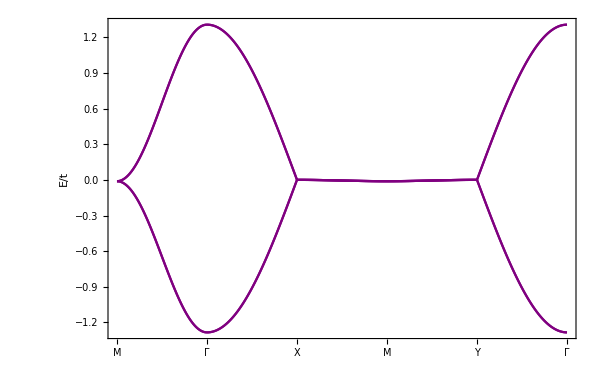

```mathematica
Vddπ = -1.0; Vddσ = 1.5; Vddδ = 0.25; θ=28.5*Pi/180;
ϵ00[θ_,kx_,ky_]:=2/3(Vddπ+Vddδ+Vddπ Cos[2 θ]^2+Vddσ Sin[2θ]^2)( Cos[kx]+Cos[ky]);
ϵ0x[θ_,kx_,ky_]:=4/3((Vddπ+Vddδ) Cos[2θ]+Vddσ Cos[2θ]^2-Vddπ Sin[2θ]^2)Cos[kx/2]Cos[ky/2];
ϵzy[θ_,kx_, ky_]:=4/3 (Vddπ+Vddδ) Sin[2θ]Cos[kx/2]Cos[ky/2];


isb4[θ_,kx_,ky_]:=({{ϵ00[θ,kx,ky], ⅇ^(-ⅈ kx) (ϵ0x[θ,kx,ky]-ⅈ ϵzy[θ,kx,ky]), 0, 0}, {ⅇ^(ⅈ kx) (ϵ0x[θ,kx,ky]+ⅈ ϵzy[θ,kx,ky]), ϵ00[θ,kx,ky], 0, 0}, {0, 0, ϵ00[θ,kx,ky], ⅇ^(-ⅈ kx) (ϵ0x[θ,kx,ky]+ⅈ ϵzy[θ,kx,ky])}, {0, 0, ⅇ^(ⅈ kx) (ϵ0x[θ,kx,ky]-ⅈ ϵzy[θ,kx,ky]), ϵ00[θ,kx,ky]}});


h[θ_,kx_,ky_]:=N[isb4[θ,kx,ky]];



div=100;
(*(*kx=0-> Pi, ky=0*)
mc2D1=Table[0,{i,1,101}];
For[i=0,i≤Pi,i=i+Pi/div,
j=0;
mc2D1[[Simplify[(i)(div/(Pi))+1]]]=h[i,j];
]
u2D1=Table[0,{i,1,101}];
For[i=1,i≤101,i++,
u2D1[[i]]={Simplify[(i-1)(Pi/div)],0,Sort[Re[Eigenvalues[mc2D1⟦i⟧]],Greater]}
]
data2D1=Table[Table[{u2D1[[i]][[1]],u2D1[[i]][[3]][[j]]},{i,1,101}],{j,1,6}];*)
(*kx= -Pi -> Pi, ky = 0, (θ, ϕ) = +x *)
mc2D1=Table[0,{i,1,div+1}];
For[i=0,i≤Pi,i=i+Pi/(div),
mc2D1[[Simplify[(i)(div/(Pi))+1]]]=h[θ,Pi-i,Pi-i];
]
u2D1=Table[0,{i,1,div+1}];
For[i=1,i≤div+1,i++,
u2D1[[i]]={Pi-Simplify[(i-1)(Pi/(div))],Pi-Simplify[(i-1)(Pi/(div))],Sort[Re[Eigenvalues[mc2D1⟦i⟧]],Greater]}
]
data2D1=Table[Table[{Pi-u2D1[[i]][[1]],u2D1[[i]][[3]][[j]]},{i,1,div+1}],{j,1,4}];

mc2D2=Table[0,{i,1,div+1}];
For[i=0,i≤Pi,i=i+Pi/(div),
mc2D2[[Simplify[(i)(div/(Pi))+1]]]=h[θ,i,0];
]
u2D2=Table[0,{i,1,div+1}];
For[i=1,i≤div+1,i++,
u2D2[[i]]={Simplify[(i-1)(Pi/(div))],0,Sort[Re[Eigenvalues[mc2D2⟦i⟧]],Greater]}
]
data2D2=Table[Table[{Pi+u2D2[[i]][[1]],u2D2[[i]][[3]][[j]]},{i,1,div+1}],{j,1,4}];


mc2D3=Table[0,{i,1,div+1}];
For[i=0,i≤Pi,i=i+Pi/div,
mc2D3[[Simplify[(i)(div/(Pi))+1]]]=h[θ,Pi,i];
]
u2D3=Table[0,{i,1,div+1}];
For[i=1,i≤div+1,i++,
u2D3[[i]]={Pi,Simplify[(i-1)(Pi/div)],Sort[Re[Eigenvalues[mc2D3⟦i⟧]],Greater]}
]
data2D3=Table[Table[{u2D3[[i]][[2]]+2Pi,u2D3[[i]][[3]][[j]]},{i,1,div+1}],{j,1,4}];


mc2D4=Table[0,{i,1,div+1}];
For[i=0,i≤Pi,i=i+Pi/div,
mc2D4[[Simplify[(i)(div/(Pi))+1]]]=h[θ,Pi-i,Pi];
]
u2D4=Table[0,{i,1,div+1}];
For[i=1,i≤div+1,i++,
u2D4[[i]]={Pi-Simplify[(i-1)(Pi/div)],Pi,Sort[Re[Eigenvalues[mc2D4⟦i⟧]],Greater]}
]
data2D4=Table[Table[{4Pi-u2D4[[i]][[1]],u2D4[[i]][[3]][[j]]},{i,1,div+1}],{j,1,4}];



mc2D5=Table[0,{i,1,div+1}];
For[i=0,i≤Pi,i=i+Pi/div,
mc2D5[[Simplify[(i)(div/(Pi))+1]]]=h[θ,0,Pi-i];
]
u2D5=Table[0,{i,1,div+1}];
For[i=1,i≤div+1,i++,
u2D5[[i]]={0,Pi-Simplify[(i-1)(Pi/div)],Sort[Re[Eigenvalues[mc2D5⟦i⟧]],Greater]}
]
data2D5=Table[Table[{5Pi-u2D5[[i]][[2]],u2D5[[i]][[3]][[j]]},{i,1,div+1}],{j,1,4}];







ListPlot[{data2D1⟦1⟧,data2D1⟦2⟧,data2D1⟦3⟧,data2D1⟦4⟧,data2D2⟦1⟧,data2D2⟦2⟧,data2D2⟦3⟧,data2D2⟦4⟧,data2D3⟦1⟧,data2D3⟦2⟧,data2D3⟦3⟧,data2D3⟦4⟧,data2D4⟦1⟧,data2D4⟦2⟧,data2D4⟦3⟧,data2D4⟦4⟧,data2D5⟦1⟧,data2D5⟦2⟧,data2D5⟦3⟧,data2D5⟦4⟧},Joined->True,Frame->True,PlotStyle->{Purple,Purple,Purple,Purple(*CMYKColor[0.8,0,0.3,0],CMYKColor[0.8,0,0.3,0],CMYKColor[0.8,0,0.3,0],CMYKColor[0.8,0,0.3,0]*)},FrameStyle->Directive[FontSize->30],PlotRange->All,FrameTicks->{{Automatic,None},{{{0,"M"},{Pi,"Γ"},{2Pi,"X"},{3Pi,"M"},{4Pi,"Y"},{5Pi,"Γ"}},None}},Axes->{False,False},GridLines->{{0,Pi,2Pi,3Pi,4Pi,5Pi},{0.0}},FrameLabel->{None,Style["E/t",FontSize->30]},GridLinesStyle->Dashed,ImageSize->600]
```

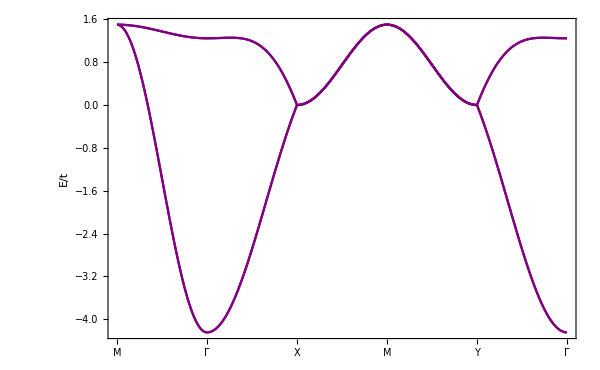

```mathematica
(* 75 *)
```

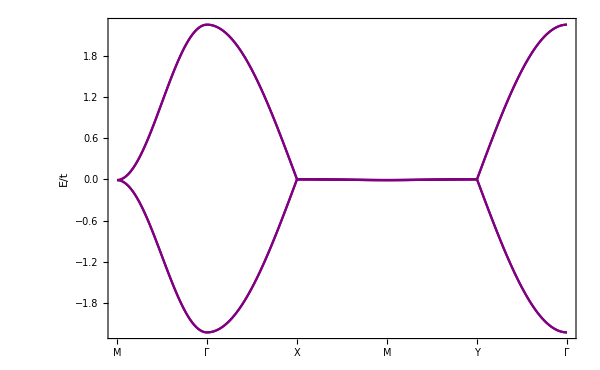

```mathematica
(* 61.5 *)
```

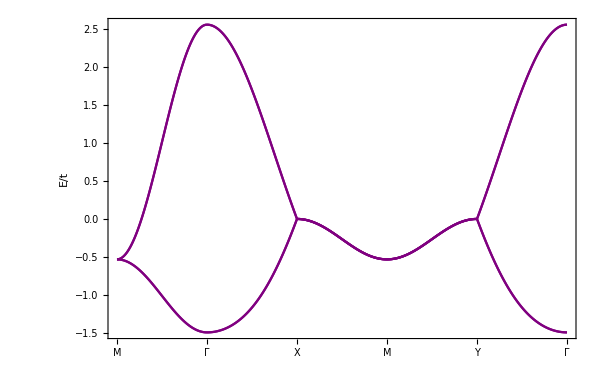

```mathematica
(* 56 *)
```

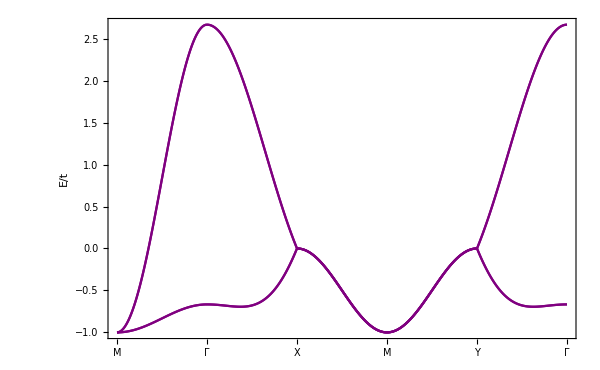

```mathematica
(* 45 *)
```

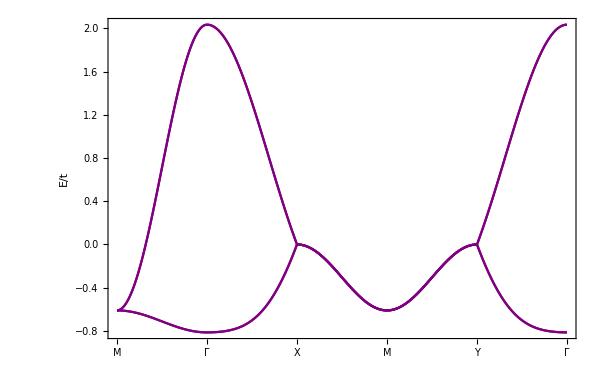

```mathematica
(* 35 *)
```

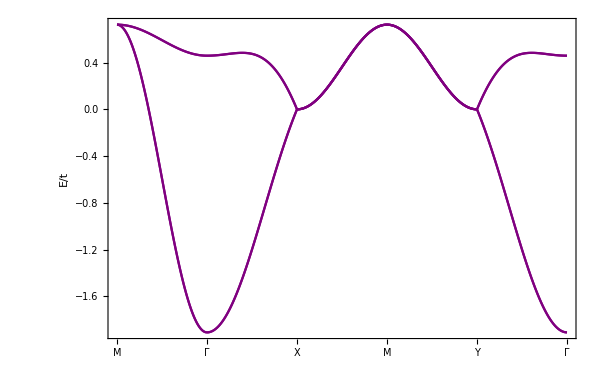

```mathematica
(* 22 *)
```

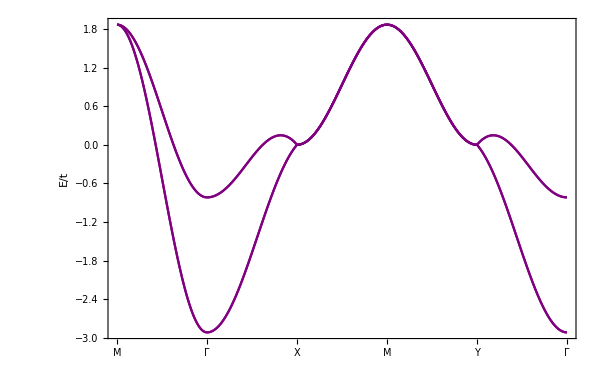

```mathematica
(* 11 *)
```

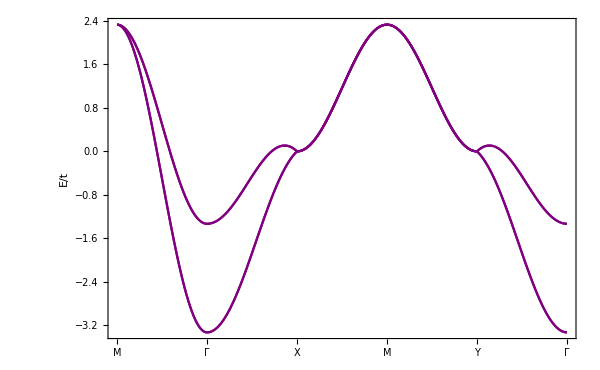

```mathematica
(* 0 *)
```

```mathematica
(* 28.5 *)
```

-Graphics-

```mathematica
61.5-28.5
```

33.